{{0,0},{1,1},{2,1},{3,1},{4,1},{5,0}}

{{0,0},{1,-1},{2,-1},{3,-1},{4,-1},{5,0}}

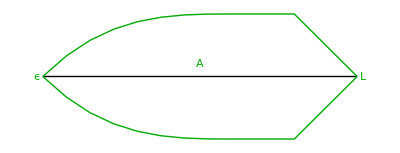

```mathematica
$pts={{0,0},{1,1},{2,1},{3,1},{4,1},{5,0}}
$pts1={#[[1]],-#[[2]]}&/@$pts
Graphics[{Line[{{0,0},{5,0}}],Darker[Green],BezierCurve[$pts],BezierCurve[$pts1],Inset[A,{2.5,0.2}],Inset[ϵ,{-.1,0}],Inset[L,{5.1,0}]}]
```

```mathematica
Graphics[{
FaceForm[{White,Opacity[0.]}],EdgeForm[{Green,Opacity[1]}],Rectangle[{-1+.1,-1+.1},{1+.1,1+.1}],
FaceForm[{White,Opacity[1.]}],EdgeForm[{Darker[Green]}],
Rectangle[{-1,-1},{1,1}],
Red,Thick,
Arrowheads[{-.02,.02}],Arrow[{{-.5,0},{.5,0}}],
Inset[A,{0,0.15}]}]
```

-Graphics-

```mathematica
Graphics[{FaceForm[{Pink,Opacity[0.]}],EdgeForm[{Green}],Rectangle[{-1,-1},{1,1}],
Darker[Green],(*
Line[{{0,-1},{0,1}}],*)
Dashed,
Line[{{-1,1},{1,-1}}],
Line[{{-1,-1},{1,1}}],
Black,
Inset[Style[A,Medium],{-.5,0}],
Inset[Style[B,Medium],{ .5,0}]
}]
```

-Graphics-

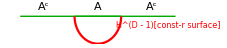

```mathematica
$f:=-.3 {Cos[#],Sin[#]}&
Show[Graphics[{
Darker[Green],
Line[{{-1,0},{1,0}}],
Thick,
Line[{{-.3,0},{.3,0}}],
Black,
Inset[Style["A",Medium],{0,0.1}],
Inset[Style["A^c",Medium],{ .7,0.1}],
Inset[Style["A^c",Medium],{ -.7,0.1}],
Red,
Inset[Style["H^(D - 1)[const-r surface]",8],{ .9,-0.1}]
}],
ParametricPlot[$f[t],{t,0,π},PlotStyle->{Red}]
]
```

```mathematica
Graphics[{
Green,
Circle[{0,0},1],
Thick,Blue,Circle[{0,0},1,{Pi/2,Pi/4}],
Red,BezierCurve[{{0,1},{.2  Sin[π/8],.2 Cos[π/8]},{Sin[π/4],Cos[π/4]}}],
Black,
Inset[Style[A,Medium],{0.5,.95}],
Inset[Style[A^c,Green,Medium],{ 1.1,0.1}],
Inset[Style[r[A],Medium],{.8  Sin[π/8],.8 Cos[π/8]}],
Red,Inset[Style[m[A],Medium],{.5  Sin[π/8],.5 Cos[π/8]}]
}]
```

-Graphics-

```mathematica
Graphics3D[{Blue,FaceForm[{Pink,Opacity[0.1]}],EdgeForm[{Thick,Blue}],
Cylinder[{{0,0,1},{0,0,1.001}},1],
Cylinder[{{0,0,-1},{0,0,-1.001}},1],
Text[Style["A"],{0,0,1}],
Text[Style["B"],{0,0,-1}],
Text[Style["BH"],{0,0,0}],
EdgeForm[{Thick,Red}],
FaceForm[{Pink,Opacity[0.]}],
Cylinder[{{0,0,0},{0,0,.001}},.5],
Arrowheads[0],Arrow[BSplineCurve[{{01,0,-1},{0.02,0,0},{1,0,1}}]],
Arrow[BSplineCurve[{{-1,0,-1},{-0.02,0,0},{-1,0,1}}]]
}
]
```

-Graphics3D-

```mathematica
Graphics3D[{Blue,FaceForm[{Pink,Opacity[0.4]}],EdgeForm[{Thick,Green}],
Cylinder[{{0,0,0},{0,0,.01}},1],
FaceForm[{Blue,Opacity[0.1]}],
Cone[{{0,0,0},{0,0,1}},1],
Cone[{{0,0,0},{0,0,-1}},1],
Red,Thick,Opacity[1],
Arrow[BSplineCurve[{{0,0,-1},{.7,.7,0},{0,0,1}}]],
Arrow[BSplineCurve[{{0,0,-1},{-.7,-.7,0},{0,0,1}}]],
Text[Style["time translations"],{0,0,1}],
Black,Text[Style[A,Large],{0,0,0}]

}
]
```

-Graphics3D-

```mathematica
Graphics3D[{Blue,FaceForm[{Pink,Opacity[0.4]}],EdgeForm[{Thick,Green}],
Cylinder[{{0,0,0},{0,0,.01}},1],
FaceForm[{Blue,Opacity[0.1]}],
Cone[{{0,0,0},{0,0,1}},1],
Cone[{{0,0,0},{0,0,-1}},1],
Red,Thick,Opacity[1],
Arrow[BSplineCurve[{{0,0,-1},{.7,.7,0},{0,0,1}}]],
Arrow[BSplineCurve[{{0,0,-1},{-.7,-.7,0},{0,0,1}}]],
Text[Style["time translations"],{0,0,1}],
Black,Text[Style[A,Large],{0,0,0}]

}
]
```

-Graphics3D-

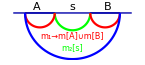

```mathematica
$fs:=-.3 {Cos[#],Sin[#]}&
$fA:=-.25 {Cos[#],Sin[#]}-{.55,0}&
$fB:=-.25 {Cos[#],Sin[#]}+{.55,0}&
$fAsB:=-.8{Cos[#],Sin[#]}&
Show[Graphics[{
Darker[Blue],Line[{{-1,0},{1,0}}],
Thick,
Line[{{-.8,0},{-.3,0}}],
Line[{{.3,0},{.8,0}}],
Black,
Inset[Style["s",Medium],{0,0.1}],
Inset[Style["B",Medium],{ .6,0.1}],
Inset[Style["A",Medium],{ -.6,0.1}],
Red,
Inset[Style["m_1→m[A]∪m[B]",8,Red],{ .0,-0.4}],
Inset[Style["m_2[s]",8,Green],{ .0,-0.6}]
}],
ParametricPlot[$fs[t],{t,0,π},PlotStyle->{Green}],
ParametricPlot[$fA[t],{t,0,π},PlotStyle->{Red}],
ParametricPlot[$fB[t],{t,0,π},PlotStyle->{Red}],
ParametricPlot[$fAsB[t],{t,0,π},PlotStyle->{Blue}]
]
```

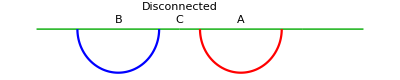

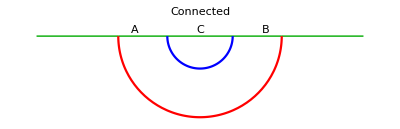

```mathematica
Clear[$f]
$f[r_,t_]:=- r{Cos[t],Sin[t]}
$ff[r_,t_]:=- r{Cos[t]+3,Sin[t]}
Show[Graphics[{
Darker[Green],
Line[{{-1,0},{-.3,0}}],
Line[{{-.3,0},{.3,0}}],
Line[{{.3,0},{.6,0}}],
Black,
Inset[Style["A",Medium],{0,0.04}],
Inset[Style["C",Medium],{ -.3,0.04}],
Inset[Style["B",Medium],{ -.6,0.04}],
Inset[Style["Disconnected",Medium],{ -.3,0.1}]
}],
ParametricPlot[$f[.2,t],{t,0,π},PlotStyle->{Red}],
ParametricPlot[$ff[.2,t],{t,0,π},PlotStyle->{Blue}]
]
Show[Graphics[{
Darker[Green],
Line[{{-1,0},{-.5,0}}],
Line[{{-.5,0},{.5,0}}],
Line[{{.5,0},{1,0}}],
Black,
Inset[Style["C",Medium],{0,0.04}],
Inset[Style["B",Medium],{ .4,0.04}],
Inset[Style["A",Medium],{ -.4,0.04}],
Inset[Style["Connected",Medium],{ -.0,0.15}]
}],
ParametricPlot[$f[.5,t],{t,0,π},PlotStyle->{Red}],
ParametricPlot[$f[.2,t],{t,0,π},PlotStyle->{Blue}]
]
```

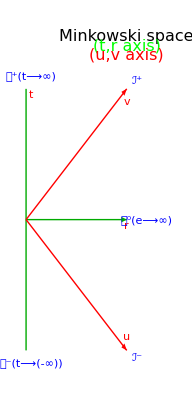

```mathematica
Graphics[{FaceForm[{Pink,Opacity[0.]}],EdgeForm[{Green}],
Darker[Green],
Line[{{0,1},{0,-1}}],
Arrow[{{0,0},{1,0}}],Inset[Style[r,Medium,Red],{1.0,0-.05}],
Inset[Style["𝒾^0(e⟶∞)",Medium,Blue],{ 1+.2,-0+.0}],
Red,Thick,
Arrow[{{0,0},{1,-1}}],Inset[Style[v,Medium,Red],{1,1-.1}],
Inset[Style[SuperPlus[ℐ],Medium,Large,Blue],{ 1+.1,1+.06}],
Arrow[{{0,0},{1,1}}],Inset[Style[u,Medium,Red],{1,-1+.1}],
Inset[Style[SuperMinus[ℐ],Medium,Large,Blue],{ 1+.1,-1-.06}],
Black,
Inset[Style[t,Medium,Red],{ 0+.05,1-.05}],
Inset[Style[SuperPlus[𝒾][t⟶∞],Medium,Blue],{ 0+.05,1+.1}],
Inset[Style[SuperMinus[𝒾][t⟶-∞],Medium,Blue],{ 0+.05,-1-.1}],
Inset[Style["Minkowski space",Medium,FontSize->16,Black],{ 1+.0,1+.4}],
Inset[Style["(t,r axis)",Medium,FontSize->16,Green],{ 1+.0,1+.33}],
Inset[Style["(u,v axis)",Medium,FontSize->16,Red],{ 1+.0,1+.26}]
}]
```

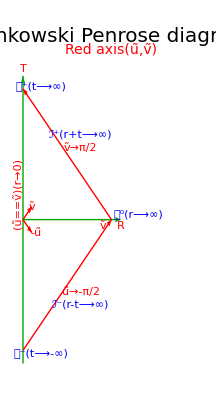

```mathematica
Graphics[{FaceForm[{Pink,Opacity[0.]}],EdgeForm[{Green}],Darker[Green],
Arrow[{{0,-1.1},{0,1.1}}],Inset[Style[T,Medium,Red],{ 0+.0,1+.15}],
Arrow[{{0,0},{1.1,0}}],Inset[Style[R,Medium,Red],{1.1,0-.05}],
Inset[Style[Rotate[(ũ==ṽ)[r->0],90 Degree],Red],{-.05,.2}],
Inset[Style["𝒾^0(r⟶∞)",Medium,Blue],{ 1+.3,0+.04}],
Inset[Style["𝒾^+(t⟶∞)",Medium,Blue],{ 0+.2,1.02}],
Inset[Style["𝒾^-(t⟶-∞)",Medium,Blue],{ 0+.2,-1.02}],
Red,
Arrow[{{1,0},{0,1}}],
Inset[Style[ṽ->π/2,Medium,Red],{.65,.55}],
Inset[Style[SuperPlus[ℐ][r+t⟶∞],Medium,Blue],{ .645,.65}],
Arrow[{{0,-1},{1,0}}],
Inset[Style[ṽ,Medium,Red],{.9,-.05}],
Inset[Style[ũ->-π/2,Medium,Red],{.65,-.55}],
Inset[Style[SuperMinus[ℐ][r-t⟶∞],Medium,Blue],{ .645,-.65}],
Arrow[{{0,0},{.1,.1}}],
Inset[Style[ṽ,Medium,Red],{.1,.1}],

Arrow[{{0,0},{.1,-.1}}],
Inset[Style[-ũ,Medium,Red],{.15,-.1}],

Inset[Style["Minkowski Penrose diagram",Medium,FontSize->20,Black],{ 1+.0,1+.4}],
Inset[Style["Red axis"[ũ,ṽ],Medium,FontSize->14,Red],{ 1+.0,1+.3}],

}]
```